```mathematica
stackHam[triv_, topo_, L_, ls_, l_,t1_,t2_, dim_]:=Module[{model, cidInc, pos, posUnit,temp, hopTriv, hopTopo, hop, newHopCoor1,newHopCoor2},

model["L"]=Merge[topo["L"],{L}];
model["nSL"]=2 topo["nSl"];
model["D"]=2 L topo["D"];
cidInc=topo["D"];

posUnit=topo["Pos"];
pos={posUnit};

Do[
temp=posUnit;
temp[[;;,dim]]=posUnit[[;;,dim]]+l n + ls ns;
AppendTo[pos,temp];
,{n,0,L-1},{ns,0,1}];
pos=Flatten[pos,1];

model["Pos"]=pos;

hopTriv=triv["Hop"];
hopTopo=topo["Hop"];

hop={};

Do[

If[ns==0,
AppendTo[hop,hopTopo];
,
AppendTo[hop,hopTriv];
];

hopTriv[[;;,2]]=hopTriv[[;;,2]]+cidInc;
hopTopo[[;;,2]]=hopTopo[[;;,2]]+cidInc;

,{n,0,L-1},{ns,0,1}];
hop=Flatten[hop,1];

newHopCoor1=Flatten[Table[{id+2 lz cidInc,id+2 lz cidInc+cidInc},{id,cidInc+1,2 cidInc},{lz,0,L-2}],1];
newHopCoor2=Flatten[Table[{id+2 lz cidInc+cidInc,id+2 lz cidInc},{id,cidInc+1,2 cidInc},{lz,0,L-2}],1];
AppendTo[hop,{I t1, newHopCoor1}];
AppendTo[hop,{-I t1, newHopCoor2}];

newHopCoor1=Flatten[Table[{id+2 lz cidInc,id+2 lz cidInc+cidInc},{id, cidInc},{lz,0,L-1}],1];
newHopCoor2=Flatten[Table[{id+2 lz cidInc+cidInc,id+2 lz cidInc},{id, cidInc},{lz,0,L-1}],1];
AppendTo[hop,{I t2, newHopCoor1}];
AppendTo[hop,{-I t2, newHopCoor2}];

model["Hop"]=hop;
model

];
```

```mathematica
constructHam[model_]:=Module[{ham,hop,dim,cond,t,coor},

dim=model["D"];
hop=model["Hop"];
cond={};
Do[
t=i[[1]];
coor=i[[2]];
AppendTo[cond,(#-> t&/@coor)];
,{i,hop}];
cond=Flatten[cond,2];
ham=SparseArray[cond];

ham

]
```

```mathematica
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];
```

```mathematica
Clear[t1,t2];
t1=-1;t2=0;
L=5;
sInc=0.5;
Inc=1.5; 
lsx={0.5,0,0};
lsy={0,0.5,0};
lsz={0,0,0.5};

lx=3  {0.5,0,0};
ly=3  {0,0.5,0};
lz=3  {0,0,0.5};

topoModel["L"]={L};
topoModel["nSl"]=2;
topoModel["D"]=2 L;
topoModel["Pos"]=Flatten[Table[(ns-1) lsx+ (n-1) lx,{n,L}, {ns,2}],1];
topoModel["Hop"]={{I t1,Table[{2l,2l+1},{l,L-1}]} ,{-I t1,Table[{2l+1,2l},{l,L-1}]} ,{I t2,Table[{2l-1,2l},{l,L}]},{-I t2,Table[{2l,2l-1},{l,L}]}};
```

```mathematica
Clear[t1,t2];
t1=0.3;t2=1.2;
trivModel["L"]={L};
trivModel["nSl"]=2;
trivModel["D"]=2 L;
trivModel["Pos"]=Flatten[Table[(ns-1) lsx+ (n-1) lx,{n,L}, {ns,2}],1];
trivModel["Hop"]={{I t1,Table[{2l,2l+1},{l,L-1}]} ,{-I t1,Table[{2l+1,2l},{l,L-1}]} ,{I t2,Table[{2l-1,2l},{l,L}]},{-I t2,Table[{2l,2l-1},{l,L}]}};
```

```mathematica
Clear[t1,t2];
t1=0;t2=1;
trivModelPer1D["L"]={L};
trivModelPer1D["nSl"]=2;
trivModelPer1D["D"]=2 L;
trivModelPer1D["Pos"]=Flatten[Table[(ns-1) lsx+ (n-1) lx,{n,L}, {ns,2}],1];
trivModelPer1D["Hop"]={{I t1,Table[{2l,2l+1},{l,L-1}]} ,{-I t1,Table[{2l+1,2l},{l,L-1}]} ,{I t2,Table[{2l-1,2l},{l,L}]},{-I t2,Table[{2l,2l-1},{l,L}]}};
```

```mathematica
trivModelPer2D=stackHam[trivModel,topoModel,L,sInc,Inc,0,1,2];
triv2DHam=constructHam[trivModelPer2D];
Sort[Abs[Eigenvalues[triv2DHam]]]
```

Merge::list1: The argument 5 is not a valid list of Associations or rules or lists of rules.

{0.204872,0.204872,0.204872,0.204872,0.204872,0.204872,0.204872,0.204872,0.204872,0.204872,0.517597,0.517597,0.517597,0.517597,0.517597,0.517597,0.517597,0.517597,0.517597,0.517597,0.821012,0.821012,0.821012,0.821012,0.821012,0.821012,0.821012,0.821012,0.821012,0.821012,1.0828,1.0828,1.0828,1.0828,1.0828,1.0828,1.0828,1.0828,1.0828,1.0828,1.27464,1.27464,1.27464,1.27464,1.27464,1.27464,1.27464,1.27464,1.27464,1.27464,1.82709,1.82709,1.82709,1.82709,1.82709,1.82709,1.82709,1.82709,1.82709,1.82709,1.83751,1.83751,1.83751,1.83751,1.83751,1.83751,1.83751,1.83751,1.83751,1.83751,1.89079,1.89079,1.89079,1.89079,1.89079,1.89079,1.89079,1.89079,1.89079,1.89079,1.92518,1.92518,1.92518,1.92518,1.92518,1.92518,1.92518,1.92518,1.92518,1.92518,1.94494,1.94494,1.94494,1.94494,1.94494,1.94494,1.94494,1.94494,1.94494,1.94494}

```mathematica
modelTop2D=stackHam[trivModel,topoModel,L,sInc,Inc,0.9,0,2];
HamTop2D=constructHam[modelTop2D];
Eigenvalues[HamTop2D]//Abs//Sort
```

Merge::list1: The argument 5 is not a valid list of Associations or rules or lists of rules.

{0.,0.,0.136213,0.136213,0.136213,0.136213,0.136213,0.136213,0.136213,0.136213,0.48109,0.48109,0.48109,0.48109,0.48109,0.48109,0.48109,0.48109,0.782613,0.782613,0.782613,0.782613,0.782613,0.782613,0.782613,0.782613,0.94739,0.94739,1.,1.,1.,1.,1.,1.,1.,1.,1.03715,1.03715,1.03715,1.03715,1.03715,1.03715,1.03715,1.03715,1.07025,1.07025,1.21968,1.21968,1.21968,1.21968,1.21968,1.21968,1.21968,1.21968,1.22488,1.22488,1.36733,1.36733,1.4653,1.4653,1.75548,1.75548,1.75548,1.75548,1.75548,1.75548,1.75548,1.75548,1.7595,1.7595,1.7595,1.7595,1.7595,1.7595,1.7595,1.7595,1.81116,1.81116,1.81116,1.81116,1.81116,1.81116,1.81116,1.81116,1.83413,1.83413,1.83413,1.83413,1.83413,1.83413,1.83413,1.83413,1.84725,1.84725,1.84725,1.84725,1.84725,1.84725,1.84725,1.84725}

```mathematica
modelTop3D=stackHam[trivModelPer2D,modelTop2D,L,sInc,Inc,0.4,0,3];
HamTop3D=constructHam[modelTop3D];
{evals,evecs}=orderedEigensystem[HamTop3D];
```

Merge::list1: The argument Merge[{5},{5}] is not a valid list of Associations or rules or lists of rules.

Eigensystem::arh: Because finding 1000 out of the 1000 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{{-2.28652,-2.28652,-2.28652,-2.28652,-2.27036,-2.27036,-2.27036,-2.27036,-2.24955,-2.24955,-2.24955,-2.24955,-2.24275,-2.24275,972,2.24275,2.24275,2.24955,2.24955,2.24955,2.24955,2.27036,2.27036,2.27036,2.27036,2.28652,2.28652,2.28652,2.28652},{1}}
 |  |  |  |

```mathematica
Length[evals]
```

1000

```mathematica
evals[[501]]
```

0.

```mathematica
evecs[[;;,501]]//Chop
evecs[[;;,500]]//Chop
```

{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Graphics3D[Point[modelTop2D["Pos"]]]
```

-Graphics3D-

```mathematica
Graphics3D[Point[modelTop3D["Pos"]]]
```

-Graphics3D-

```mathematica
a={3};
AppendTo[a,4];
```

```mathematica
a
```

AppendTo[{},3]

```mathematica
HamTopo=constructHam[topoModel];
HamTriv=constructHam[trivModel];
```

```mathematica
Ham
```

SparseArray[…]

```mathematica
Eigenvalues[N[HamTopo]]
```

{-1.,-1.,-1.,1.,1.,1.,0.,0.}

```mathematica
Eigenvalues[N[HamTriv]]
```

{-1.4497,1.4497,-1.31219,1.31219,1.12846,-1.12846,-0.965967,0.965967}

```mathematica
Flatten[{{{2,3}->t1,{4,5}->t1,{6,7}->t1},{{1,2}->t2,{3,4}->t2,{5,6}->t2,{7,8}->t2}},2]
```

{{2,3}→t1,{4,5}→t1,{6,7}→t1,{1,2}→t2,{3,4}→t2,{5,6}→t2,{7,8}→t2}

```mathematica
topoModel["Pos"]=#+vInc&/@topoModel["Pos"]
```

{{0.,0,1.},{0.5,0,1.},{1.5,0,1.},{2.,0,1.},{3.,0,1.},{3.5,0,1.},{4.5,0,1.},{5.,0,1.}}

{{0.,0,1.},{0.5,0,1.},{1.5,0,1.},{2.,0,1.},{3.,0,1.},{3.5,0,1.},{4.5,0,1.},{5.,0,1.}}

```mathematica
Do[
v=topoModel["Pos"][[i,;;]];
Print[v,i]
topoModel["Pos"][[i,;;]]=v+{0,0,10.};,{i,Length[topoModel["Pos"]]}];
```

{0.,0,0}1

Set::write: Tag Times in Null {0.,0,0} is Protected.

{0.5,0,0}2

Set::write: Tag Times in Null {0.5,0,0} is Protected.

{1.5,0,0}3

Set::write: Tag Times in Null {1.5,0,0} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{2.,0,0}4

{3.,0,0}5

{3.5,0,0}6

{4.5,0,0}7

{5.,0,0}8

```mathematica
topoModel["Pos"][[1,;;]]=topoModel["Pos"][[1,;;]]
```

Set::setps: topoModel[Pos] in the part assignment is not a symbol.

{0.,0,0}

```mathematica
vInc={0,0,1.};
topoModel["Pos"][[;;,3]=topoModel["Pos"][[;;,3]]+10
```

{10,10,10,10,10,10,10,10}

```mathematica
topoModel["Pos"]
```

{{0.,0,0},{0.5,0,0},{1.5,0,0},{2.,0,0},{3.,0,0},{3.5,0,0},{4.5,0,0},{5.,0,0}}

```mathematica
topoModel["Pos"]+{0,0.,10.}
```

Thread::tdlen: Objects of unequal length in {{0.,0,0},{0.5,0,0},{1.5,0,0},{2.,0,0},{3.,0,0},{3.5,0,0},{4.5,0,0},{5.,0,0}}+{0,0.,10.} cannot be combined.

{0,0.,10.}+{{0.,0,0},{0.5,0,0},{1.5,0,0},{2.,0,0},{3.,0,0},{3.5,0,0},{4.5,0,0},{5.,0,0}}

{{0.,0,0},{0.5,0,0},{1.5,0,0},{2.,0,0},{3.,0,0},{3.5,0,0},{4.5,0,0},{5.,0,0}}

## NEGF

{1,2}

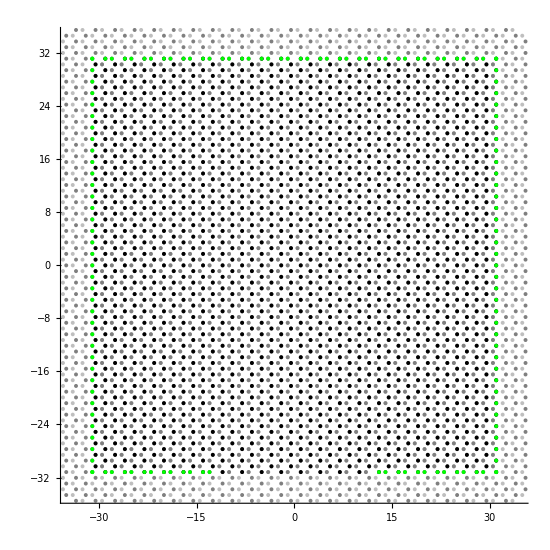

```mathematica
nuc=21;t=1.0;
width=3*nuc;height=width;inFrac=0.4;
L=Max[{width,height}];
a=1;L1=L+1;L2=L+1;
a1=a/2{3,√3,0};
a2=a/2{3,-√3,0};
b1={a,0,0};
uc = {0*b1,b1};
ucid={1,2}
latt=Flatten[Table[{n1*a1+n2*a2+uc[[i]],ucid[[i]]},{n1,L1},{n2,L2},{i,Length[uc]}],2];
meanPosition=Mean[latt[[All,1]]];
latt[[All,1]]=(#-meanPosition)&/@latt[[All,1]];
lattRegion=DeleteCases[latt,_?(Not[(-width/2<#[[1,1]]<width/2)&&(-height/2<#[[1,2]]<height/2)]&)];
rB=Max[lattRegion[[All,1]][[All,1]]];lB=Min[lattRegion[[All,1]][[All,1]]];
tB=Max[lattRegion[[All,1]][[All,2]]];bB=Min[lattRegion[[All,1]][[All,2]]];
lrPos=Flatten[Position[lattRegion[[All,1]][[All,1]],n_ /; n==#]]&/@{rB,lB};
tbPos=Flatten[Position[lattRegion[[All,1]][[All,2]],n_ /; n==#]]&/@{tB,bB};bPos=Join[lrPos,tbPos];
cL=IntegerPart[Length[tbPos[[2]]]/2];
inR = IntegerPart[cL*inFrac];
inPos = tbPos[[2,cL-inR+1;;-(cL-inR+1)]];
bPos=Complement[#,inPos]&/@bPos;
col={Black,Gray};
Graphics[{{{Directive[Opacity[0.5],col[[#[[2]]]]],Disk[#[[1,1;;2]],0.3]}&/@latt},{{col[[#[[2]]]],Disk[#[[1,1;;2]],0.3]}&/@lattRegion},{{Green,Disk[#[[1,1;;2]],0.3]}&/@lattRegion[[#]]&/@bPos}(*,{{Blue,Disk[#[[1,1;;2]],0.3]}&/@lattRegion[[#]]&/@{inPos}}*)},Axes->True,PlotRange->{{-width/2-3,width/2+3},{-height/2-3,height/2+3}}]
latt=lattRegion;
dimH = Length[latt];
```

```mathematica
latt
```

{{{-31,-18 √3,0},2},{{-31,-17 √3,0},2},{{-61/2,-(35 √3)/2,0},1},{{-59/2,-(35 √3)/2,0},2},{{-29,-18 √3,0},1},{{-28,-18 √3,0},2},{{-31,-16 √3,0},2},{{-61/2,-(33 √3)/2,0},1},{{-59/2,-(33 √3)/2,0},2},{{-29,-17 √3,0},1},{{-28,-17 √3,0},2},{{-55/2,-(35 √3)/2,0},1},{{-53/2,-(35 √3)/2,0},2},{{-26,-18 √3,0},1},{{-25,-18 √3,0},2},{{-31,-15 √3,0},2},3034,{{31,15 √3,0},1},{{25,18 √3,0},1},{{26,18 √3,0},2},{{53/2,(35 √3)/2,0},1},{{55/2,(35 √3)/2,0},2},{{28,17 √3,0},1},{{29,17 √3,0},2},{{59/2,(33 √3)/2,0},1},{{61/2,(33 √3)/2,0},2},{{31,16 √3,0},1},{{28,18 √3,0},1},{{29,18 √3,0},2},{{59/2,(35 √3)/2,0},1},{{61/2,(35 √3)/2,0},2},{{31,17 √3,0},1},{{31,18 √3,0},1}}
 |  |  |  |

```mathematica
lattRegion
```

{{{-31,-18 √3,0},2},{{-31,-17 √3,0},2},{{-61/2,-(35 √3)/2,0},1},{{-59/2,-(35 √3)/2,0},2},{{-29,-18 √3,0},1},{{-28,-18 √3,0},2},{{-31,-16 √3,0},2},{{-61/2,-(33 √3)/2,0},1},{{-59/2,-(33 √3)/2,0},2},{{-29,-17 √3,0},1},{{-28,-17 √3,0},2},{{-55/2,-(35 √3)/2,0},1},{{-53/2,-(35 √3)/2,0},2},{{-26,-18 √3,0},1},{{-25,-18 √3,0},2},{{-31,-15 √3,0},2},3034,{{31,15 √3,0},1},{{25,18 √3,0},1},{{26,18 √3,0},2},{{53/2,(35 √3)/2,0},1},{{55/2,(35 √3)/2,0},2},{{28,17 √3,0},1},{{29,17 √3,0},2},{{59/2,(33 √3)/2,0},1},{{61/2,(33 √3)/2,0},2},{{31,16 √3,0},1},{{28,18 √3,0},1},{{29,18 √3,0},2},{{59/2,(35 √3)/2,0},1},{{61/2,(35 √3)/2,0},2},{{31,17 √3,0},1},{{31,18 √3,0},1}}
 |  |  |  |

```mathematica
dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt[[All,1]],latt[[All,1]],1];
```

```mathematica
Outer
```

```mathematica
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
```

```mathematica
neighbors=Position[dists,#,3]&/@ddists[[;;3]];
```

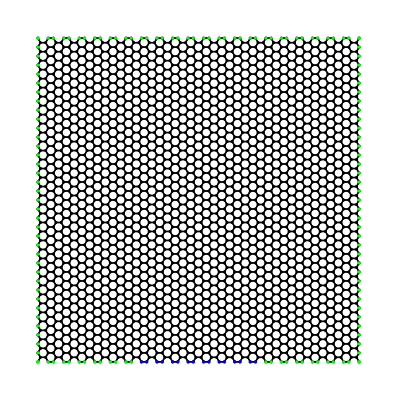

```mathematica
Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]},{Black,Disk[#[[1,1;;2]],0.3]}&/@latt,{{Green,Disk[#[[1,1;;2]],0.31]}&/@lattRegion[[#]]&/@bPos},{{Blue,Disk[#[[1,1;;2]],0.31]}&/@lattRegion[[#]]&/@{inPos}}}]
(*Graphics3D[{{{Black,CapForm["Butt"],Tube[{latt[[#[[1]]]],latt[[#[[2]]]]},.1]}&/@neighbors[[2]]},{Black,Sphere[#,0.3]}&/@latt},ViewPoint->Top];*)
```

Eigensystem::arh: Because finding 3066 out of the 3066 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

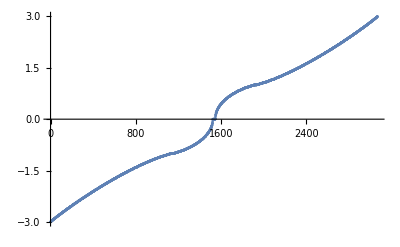

True

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];
H = SparseArray[#-> t&/@neighbors[[2]]];
{energies,wavefunctions}=orderedEigensystem[H]//Sort;
imEnergies=Im[energies];
energies=Re[energies];
ListPlot[energies]
max=Max[energies];min=Min[energies];
DeleteDuplicates[Chop[wavefunctions†.H.wavefunctions-DiagonalMatrix[energies]]//Flatten]=={0}
(*Histogram[energies,{min,max,(max-min)/54},"Probability",PlotRange->{{-1.5,1.5},Automatic}]*)
```

```mathematica
wavefunctions†.wavefunctions;
ppExact=Diagonal[{#}ᵀ.{#}*]&/@(wavefunctionsᵀ);
gsExact=({#}ᵀ.{#}*)&/@(wavefunctionsᵀ);
gsExact=gsExact/Max[gsExact];
```

```mathematica
ppExact = ppExact/Max[ppExact];
```

```mathematica
bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];

<<MaTeX`
(*Manipulate[Show[bg,Graphics[{{Directive[Opacity[#[[1]]],Red],Disk[#[[2,1;;2]],0.3]}&/@({ppExact[[i]],latt[[All,1]]}ᵀ),{{Directive[Blue,Opacity[Im[gsExact[[i,Sequence@@#]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}],PlotLabel->MaTeX[StringForm["|\\psi_{E=``t}|^2",DecimalForm[energies[[i]],{4,4}]]]],{{i,IntegerPart[Length[ppExact]/2]},1,Length[ppExact],1}]*)
```

```mathematica
{bene,bvals}=HistogramList[energies,{min,max,(max-min)/53},Probability];
ListPlot[{MovingAverage[bene,2],bvals*2*π}ᵀ,Joined->True,PlotTheme->"Scientific"]
```

```mathematica
η=1*^2;
Gs={};
ees=Range[-3,3,0.1];
ees = energies;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];
Monitor[
Do[
AppendTo[Gs,Inverse[N[H-ee*IdentityMatrix[Dimensions[H]]-Σ]]];
,{ee,ees}],ee]
Clear[BlockAverage]
BlockAverage[xs_,r_]:=Table[Mean[xs[[i;;i+r]]],{i,1,Length[xs]-r,r}]
As=Plus@@Re[Diagonal[-ⅈ*(#-#†)]]&/@Gs;
As/=Plus@@As;
rBlock=Max[IntegerPart[Length[ees]/50],1];
mAs=BlockAverage[As,rBlock];
mees=BlockAverage[ees,rBlock];
mAs/=Plus@@mAs;
ListPlot[{mees,mAs 2π}ᵀ,Joined->True,PlotRange->Full,PlotLabel->"Spectral function (block average)"]
ListPlot[{ees,As 2π}ᵀ,Joined->True,PlotRange->Full,PlotLabel->"Spectral function"]
ns = Re[Diagonal[(#+#†)]]&/@Gs;
pp = Abs[#]/If[(w=Max[Abs[#]])>1*^-8,w,1]&/@ns;
bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];(*Manipulate[Show[bg,Graphics[{{Directive[Opacity[#[[1]]],Red],Disk[#[[2,1;;2]],0.3]}&/@({pp[[i]],latt[[All,1]]}ᵀ),{{Directive[Blue,Opacity[Abs[η*Im[Gs[[i,Sequence@@#]]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],η*Im[Gs[[i,Sequence@@#]]](latt[[All,1]][[#[[2]],1;;2]]-latt[[All,1]][[#[[1]],1;;2]])+latt[[All,1]][[#[[1]],1;;2]]}]}&/@neighbors[[2]]}}],PlotLabel->MaTeX[StringForm["|\\psi_{E=``t}|^2",DecimalForm[ees[[i]],{4,4}]]]],{{i,IntegerPart[Length[pp]/2]},1,Length[pp],1}]*)
```

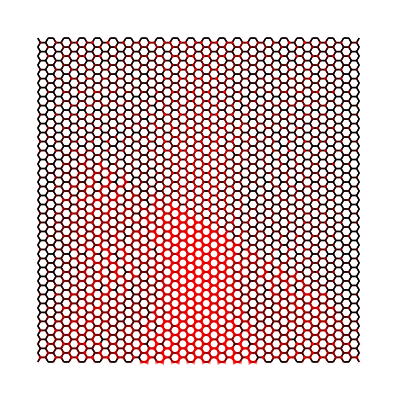

```mathematica
η=1*^1;
Σ=SparseArray[{#,#}->- ⅈ η&/@(bPos//Flatten)];

ene=0.3;
Kp={0,(+4π)/(3 √3),0};
Km={0,(-4π)/(3 √3),0};
Cp=0.0;
Cm=1.0;
kx=0;
ky=ene;
ϕ=If[ky==0,π/2,ArcTan[kx/ky]];
σ=Sign[ene];

Clear[χ]
χ[1][r_,k_,σ_,ϕ_]:=Cm*ⅇ^(ⅈ(k+Km).r)+Cp*ⅇ^(ⅈ(k+Kp).r)
χ[2][r_,k_,σ_,ϕ_]:=σ Cm ⅇ^(ⅈ(k+Km).r + ⅈ ϕ)-σ Cp ⅇ^(ⅈ(k+Kp).r - ⅈ ϕ)
inTuples=Tuples[{inPos,inPos}];
ΣinP=0*H;
(ΣinP[[Sequence@@#]]=χ[latt[[#[[1]],2]]][latt[[#[[1]],1]],{kx,ky,0},+1,ϕ]* χ[latt[[#[[2]],2]]][latt[[#[[2]],1]],{kx,ky,0},+1,ϕ])&/@inTuples;
G=Inverse[N[H-ene*IdentityMatrix[Dimensions[H]]-Σ]];
GP = G.ΣinP.G†;
GP=GP/Max[Abs[Diagonal[GP,1]]];
nP = Re[Diagonal[(GP+GP†)]];
ppP = Abs[nP]/If[(w=Max[Abs[nP]])>1*^-8,w,1];

bg=Graphics[{{{Black,CapForm["Butt"],Line[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}];
Show[bg,Graphics[{{Directive[Opacity[(#[[1]])^(1)],Red],Disk[#[[2,1;;2]],0.3]}&/@({ppP,latt[[All,1]]}ᵀ),{{Directive[Red,Opacity[Abs[Im[GP[[Sequence@@#]]]]]],CapForm["Butt"],Arrow[{latt[[All,1]][[#[[1]],1;;2]],latt[[All,1]][[#[[2]],1;;2]]}]}&/@neighbors[[2]]}}]]
```